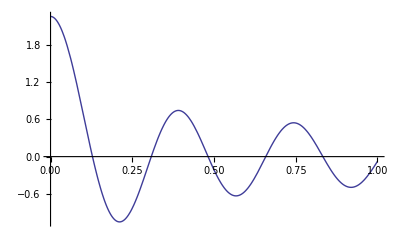

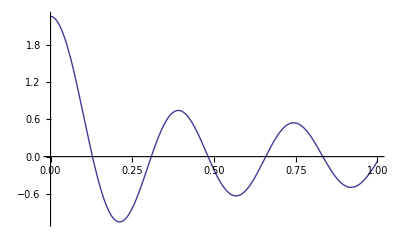

```mathematica
s1[t_]:=∑_(k=0)^50 ((I*5.7*π*t)^k*(1+(-1)^k))/Gamma[k+1.5];
s2[t_]:=2/Gamma[1.5]+∑_(k=1)^100 (2*(-1)^k*(5.7*π*t)^(2*k))/Gamma[2*k+1.5];
Plot[s1[t],{t,0,1}]
Plot[s2[t],{t,0,1}]
```

```mathematica
u[t_]:=MittagLefflerE[1,1.5,I*5.7*π*t]+MittagLefflerE[1,1.5,-I*5.7*π*t];
Plot[u[t],{t,0,1}]
```

-Graphics-

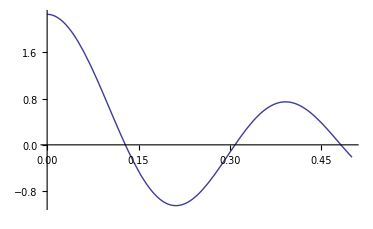

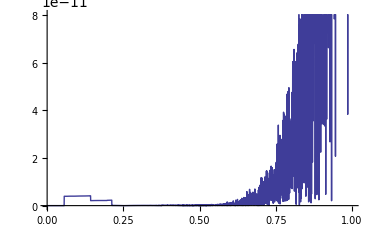

4.63848×10^-10

```mathematica
mle[a_,b_,t_]:=∑_(k=0)^100 t^k/Gamma[a*k+b];
Plot[mle[1,1.5,I*5.7*π*t]+mle[1,1.5,-I*5.7*π*t],{t,0,0.5}]
Plot[Abs[u[t]-s2[t]],{t,0,1}]
Abs[u[0.99999999]-s2[0.99999999]]
```

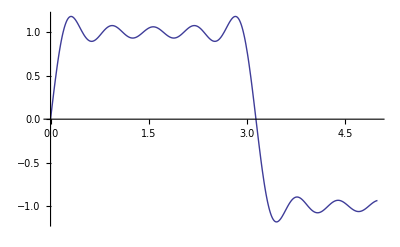

```mathematica
fourier[x_]:=4*(Sin[x]/(π)+Sin[3*x]/(3*π)+Sin[5*x]/(5*π)+Sin[7*x]/(7*π)+Sin[9*x]/(9*π))
Plot[fourier[x],{x,0,5}]
```

```mathematica
FourierSinSeries[4*Sin[7x]/(7*π),x,5]
```

0

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
ν=0.5;
m=1.;
p=6;
gsptw=GaussianQuadratureWeights[2*p+5,0,1,MachinePrecision];
gspt=gsptw[[All,1]];
(*Print[gsptw]
Print[gspt]*)
fdsine[λ_,t_]:=-0.5*I*(I*λ)^m t^(m-ν)*(MittagLefflerE[1,m-ν+1.,I*λ*t]-(-1.)^m*MittagLefflerE[1,m-ν+1.,-I*λ*t]);
fdfourier=Re[∑_(n=1)^5 1/((2*n-1)π)*fdsine[(2*n-1)*π,gspt]];
Print[fdfourier]
```

{0.386547-2.36692×10^-17 ⅈ,0.840244-5.14501×10^-17 ⅈ,1.00356-6.14501×10^-17 ⅈ,0.610906-3.74072×10^-17 ⅈ,0.19253-1.1789×10^-17 ⅈ,0.36257-2.2201×10^-17 ⅈ,0.260382-1.59438×10^-17 ⅈ,0.184286-1.12843×10^-17 ⅈ,0.26633-1.6308×10^-17 ⅈ,0.104102-6.37443×10^-18 ⅈ,0.278181-1.70337×10^-17 ⅈ,0.0547266-3.35104×10^-18 ⅈ,0.19041-1.16593×10^-17 ⅈ,0.359997-2.20435×10^-17 ⅈ,-0.123852+7.58378×10^-18 ⅈ,-0.732663+4.48627×10^-17 ⅈ,-1.05445+6.45665×10^-17 ⅈ}

{0.386547-2.36692×10^-17 ⅈ,0.840244-5.14501×10^-17 ⅈ,1.00356-6.14501×10^-17 ⅈ,0.610906-3.74072×10^-17 ⅈ,0.19253-1.1789×10^-17 ⅈ,0.36257-2.2201×10^-17 ⅈ,0.260382-1.59438×10^-17 ⅈ,0.184286-1.12843×10^-17 ⅈ,0.26633-1.6308×10^-17 ⅈ,0.104102-6.37443×10^-18 ⅈ,0.278181-1.70337×10^-17 ⅈ,0.0547266-3.35104×10^-18 ⅈ,0.19041-1.16593×10^-17 ⅈ,0.359997-2.20435×10^-17 ⅈ,-0.123852+7.58378×10^-18 ⅈ,-0.732663+4.48627×10^-17 ⅈ,-1.05445+6.45665×10^-17 ⅈ}

{0.00471226,0.0246622,0.0598804,0.109243,0.171164,0.243655,0.324384,0.410758,0.5,0.589242,0.675616,0.756345,0.828836,0.890757,0.94012,0.975338,0.995288}

{{0.00471226,0.0120742},{0.0246622,0.0277298},{0.0598804,0.0425181},{0.109243,0.0559419},{0.171164,0.0675682},{0.243655,0.0770229},{0.324384,0.0840021},{0.410758,0.0882814},{0.5,0.0897232},{0.589242,0.0882814},{0.675616,0.0840021},{0.756345,0.0770229},{0.828836,0.0675682},{0.890757,0.0559419},{0.94012,0.0425181},{0.975338,0.0277298},{0.995288,0.0120742}}

{0.00471226,0.0246622,0.0598804,0.109243,0.171164,0.243655,0.324384,0.410758,0.5,0.589242,0.675616,0.756345,0.828836,0.890757,0.94012,0.975338,0.995288}

{{0.00471226,0.0120742},{0.0246622,0.0277298},{0.0598804,0.0425181},{0.109243,0.0559419},{0.171164,0.0675682},{0.243655,0.0770229},{0.324384,0.0840021},{0.410758,0.0882814},{0.5,0.0897232},{0.589242,0.0882814},{0.675616,0.0840021},{0.756345,0.0770229},{0.828836,0.0675682},{0.890757,0.0559419},{0.94012,0.0425181},{0.975338,0.0277298},{0.995288,0.0120742}}

{{0.00471226,0.0120742},{0.0246622,0.0277298},{0.0598804,0.0425181},{0.109243,0.0559419},{0.171164,0.0675682},{0.243655,0.0770229},{0.324384,0.0840021},{0.410758,0.0882814},{0.5,0.0897232},{0.589242,0.0882814},{0.675616,0.0840021},{0.756345,0.0770229},{0.828836,0.0675682},{0.890757,0.0559419},{0.94012,0.0425181},{0.975338,0.0277298},{0.995288,0.0120742}}

{0.00471226,0.0246622,0.0598804,0.109243,0.171164,0.243655,0.324384,0.410758,0.5,0.589242,0.675616,0.756345,0.828836,0.890757,0.94012,0.975338,0.995288}